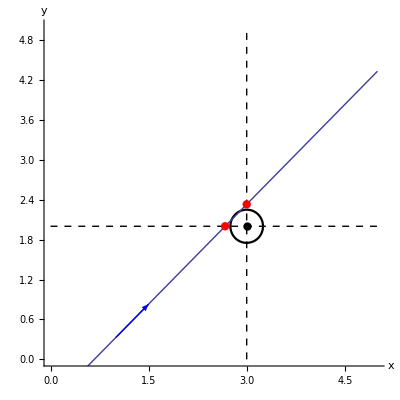

```mathematica
Show[ContourPlot[(x-3)^2+(y-2)^2==0.25^2,{x,0,5},{y,0,5},Frame->False,Axes->True,AspectRatio->1,AxesLabel->{"x","y"},ContourStyle->Directive[Thickness[0.004],Black],AxesStyle->Thickness[0.003],LabelStyle->Directive[FontFamily->"Courier",FontSize->18]],ListPlot[{{3,2}},PlotStyle->Directive[PointSize[0.015],Black]],ContourPlot[{x==3,y==2},{x,0,5},{y,0,5},ContourStyle->Dashed],Plot[x-0.67,{x,0,5}],Graphics[{Blue,Arrow[{{1,1-0.67},{1.5,1.5-0.67}}]}],ListPlot[{{2.67,2}},PlotStyle->Directive[PointSize[0.015],Red]],ListPlot[{{3,3-0.67}},PlotStyle->Directive[PointSize[0.015],Red]]]
```

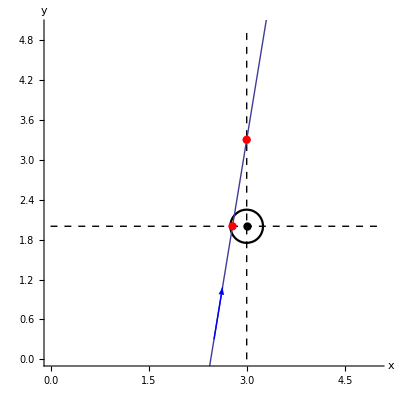

```mathematica
Show[ContourPlot[(x-3)^2+(y-2)^2==0.25^2,{x,0,5},{y,0,5},Frame->False,Axes->True,AspectRatio->1,AxesLabel->{"x","y"},ContourStyle->Directive[Thickness[0.004],Black],AxesStyle->Thickness[0.003],LabelStyle->Directive[FontFamily->"Courier",FontSize->18]],ListPlot[{{3,2}},PlotStyle->Directive[PointSize[0.015],Black]],ContourPlot[{x==3,y==2},{x,0,5},{y,0,5},ContourStyle->Dashed],Plot[6(x-2.45),{x,0,5}],Graphics[{Blue,Arrow[{{2.5,6*0.05},{2.63,6(2.63-2.45)}}]}],ListPlot[{{2.45+2/6,2}},PlotStyle->Directive[PointSize[0.015],Red]],ListPlot[{{3,6(3-2.45)}},PlotStyle->Directive[PointSize[0.015],Red]]]
```